# EllipseNormalization

## Canonical normalization of first-harmonic ellipses

## Purpose

This notebook supports the ellipse-normalization material in Chapter 3. It extracts the first-harmonic ellipse determined by c_1 and c_(n-1), computes its semi-axes and orientation, and constructs canonical affine normalizations.

All executable cells are ordinary Wolfram Language Input cells. Typeset box expressions appear only in explanatory cells.

## 1. Fourier and pair-plane definitions

```mathematica
ClearAll["Global`*"];

omega[n_Integer?Positive] := Exp[2 Pi I/n];

fourierVector[n_Integer?Positive, k_Integer] :=
  Table[omega[n]^(j k), {j, 0, n - 1}]/Sqrt[n];

fourierMatrix[n_Integer?Positive] :=
  Transpose@Table[fourierVector[n, k], {k, 0, n - 1}];

fourierCoefficients[p_List] := Module[{F},
  F = fourierMatrix[Length[p]];
  ConjugateTranspose[F] . N[p]
];

fourierSynthesis[c_List] :=
  fourierMatrix[Length[c]] . c;

centerPolygon[p_List] :=
  N[p] - Mean[N[p]];

firstHarmonicData[p_List] := Module[{n, c},
  n = Length[p];
  c = fourierCoefficients[p];
  <|
    "c1" -> c[[2]],
    "cNMinus1" -> c[[n]]
  |>
];

pairPlaneProjection[p_List] := Module[{n, c, result},
  n = Length[p];
  c = fourierCoefficients[p];
  result = ConstantArray[0, n];
  result[[2]] = c[[2]];
  result[[n]] = c[[n]];
  fourierSynthesis[result]
];
```

```mathematica
nExample = 12;
SeedRandom[4040];
pExample = RandomReal[{-1, 1}, nExample] + I RandomReal[{-1, 1}, nExample];
pExample = centerPolygon[pExample];
pEllipse = pairPlaneProjection[pExample];
```

## 2. Continuous ellipse determined by the first harmonic

Ignoring the common Fourier normalization, the first-harmonic curve is

z(t)=c_1 e^it+c_(n-1)e^-it

```mathematica
ellipseCurve[c1_, cN_, t_] :=
  c1 Exp[I t] + cN Exp[-I t];

ellipseSample[n_Integer?Positive, c1_, cN_] :=
  Table[ellipseCurve[c1, cN, 2 Pi j/n], {j, 0, n - 1}];
```

```mathematica
dataExample = firstHarmonicData[pExample];
c1Example = dataExample["c1"];
cNExample = dataExample["cNMinus1"];
```

## 3. Semi-axis lengths

The semi-axis lengths of the ellipse are

a=|c_1|+|c_(n-1)|, b=||c_1|-|c_(n-1)||

```mathematica
ellipseSemiAxesFromCoefficients[c1_, cN_] := Module[{a, b},
  a = Abs[c1] + Abs[cN];
  b = Abs[Abs[c1] - Abs[cN]];
  {a, b}
];

ellipseSemiAxes[p_List] := Module[{data},
  data = firstHarmonicData[p];
  ellipseSemiAxesFromCoefficients[data["c1"], data["cNMinus1"]]
];
```

```mathematica
axesExample = ellipseSemiAxes[pExample];
axesExample
```

{2.08021,1.1406}

## 4. Nondegeneracy and eccentricity

```mathematica
nondegenerateEllipseQ[c1_, cN_, tol_: 10^-10] :=
  TrueQ[Abs[Abs[c1] - Abs[cN]] > tol];

ellipseEccentricity[c1_, cN_] := Module[{a, b},
  {a, b} = ellipseSemiAxesFromCoefficients[c1, cN];
  If[a == 0, Indeterminate, Sqrt[Max[0, 1 - (b/a)^2]]]
];

ellipseAxisRatio[c1_, cN_] := Module[{a, b},
  {a, b} = ellipseSemiAxesFromCoefficients[c1, cN];
  If[b == 0, Infinity, a/b]
];
```

```mathematica
{
  nondegenerateEllipseQ[c1Example, cNExample],
  ellipseEccentricity[c1Example, cNExample],
  ellipseAxisRatio[c1Example, cNExample]
}
```

{True,0.836275,1.82378}

## 5. Orientation angles

Writing c_1=r_1 e^(i θ_1) and c_(n-1)=r_2 e^(i θ_2), the ellipse orientation and phase parameters are

ψ=(θ_1+θ_2)/2, δ=(θ_1-θ_2)/2

```mathematica
ellipseOrientationData[c1_, cN_] := Module[{theta1, thetaN},
  theta1 = Arg[c1];
  thetaN = Arg[cN];
  <|
    "Orientation" -> (theta1 + thetaN)/2,
    "Phase" -> (theta1 - thetaN)/2
  |>
];
```

```mathematica
orientationExample = ellipseOrientationData[c1Example, cNExample];
orientationExample
```

<|Orientation→0.499665,Phase→-1.75735|>

## 6. Axis-aligned parametrization

After removing the orientation angle, the curve becomes an axis-aligned ellipse:

e^-iψ z(t)=acos(t+δ)+ibsin(t+δ)

```mathematica
axisAlignedCurve[c1_, cN_, t_] := Module[{angles, psi},
  angles = ellipseOrientationData[c1, cN];
  psi = angles["Orientation"];
  Exp[-I psi] ellipseCurve[c1, cN, t]
];

axisAlignedModel[c1_, cN_, t_] := Module[{axes, angles, a, b, delta, sign},
  axes = ellipseSemiAxesFromCoefficients[c1, cN];
  angles = ellipseOrientationData[c1, cN];
  {a, b} = axes;
  delta = angles["Phase"];
  sign = Sign[Abs[c1] - Abs[cN]];
  a Cos[t + delta] + I sign b Sin[t + delta]
];
```

```mathematica
axisAlignmentError = Max@Table[
  Abs[N[
    axisAlignedCurve[c1Example, cNExample, t] -
    axisAlignedModel[c1Example, cNExample, t]
  ]],
  {t, 0., 2 Pi, 2 Pi/100}
];
axisAlignmentQ = axisAlignmentError < 10^-10;
```

```mathematica
axisAlignmentError
```

6.75322×10^-16

```mathematica
axisAlignmentQ
```

True

## 7. Real-linear anisotropy map

For z=x+iy, define

D_r(z)=x+iry

```mathematica
dilationD[z_, r_?NumericQ] :=
  Re[z] + I r Im[z];

inverseDilationD[z_, r_?NumericQ] :=
  Re[z] + I Im[z]/r;
```

## 8. Normalization to a circle

For a nondegenerate ellipse with semi-axes a and b, rotate by -ψ, divide by a, and scale the imaginary direction by a/b.

```mathematica
ellipseNormalizationParameters[c1_, cN_] := Module[{axes, angles, a, b},
  axes = ellipseSemiAxesFromCoefficients[c1, cN];
  angles = ellipseOrientationData[c1, cN];
  {a, b} = axes;
  If[b < 10^-12, Return[Missing["DegenerateEllipse"]]];
  <|
    "MajorAxis" -> a,
    "MinorAxis" -> b,
    "Orientation" -> angles["Orientation"],
    "Phase" -> angles["Phase"],
    "Anisotropy" -> a/b
  |>
];

normalizeEllipsePoint[z_, params_Association] := Module[{rotated},
  rotated = Exp[-I params["Orientation"]] z/params["MajorAxis"];
  dilationD[rotated, params["Anisotropy"]]
];

inverseNormalizeEllipsePoint[z_, params_Association] := Module[{undilated},
  undilated = inverseDilationD[z, params["Anisotropy"]];
  params["MajorAxis"] Exp[I params["Orientation"]] undilated
];
```

```mathematica
normalizationParamsExample = ellipseNormalizationParameters[c1Example, cNExample];
normalizationParamsExample
```

<|MajorAxis→2.08021,MinorAxis→1.1406,Orientation→0.499665,Phase→-1.75735,Anisotropy→1.82378|>

```mathematica
normalizationInverseError = Max@Table[
  Abs[N[
    inverseNormalizeEllipsePoint[
      normalizeEllipsePoint[ellipseCurve[c1Example, cNExample, t], normalizationParamsExample],
      normalizationParamsExample
    ] - ellipseCurve[c1Example, cNExample, t]
  ]],
  {t, 0., 2 Pi, 2 Pi/100}
];
normalizationInverseQ = normalizationInverseError < 10^-10;
```

```mathematica
normalizationInverseError
```

4.96507×10^-16

```mathematica
normalizationInverseQ
```

True

## 9. Normalized curve is the unit circle

```mathematica
normalizedCurve[c1_, cN_, t_, params_Association] :=
  normalizeEllipsePoint[ellipseCurve[c1, cN, t], params];

unitCircleError = Max@Table[
  Abs[N[Abs[normalizedCurve[c1Example, cNExample, t, normalizationParamsExample]] - 1]],
  {t, 0., 2 Pi, 2 Pi/100}
];
unitCircleQ = unitCircleError < 10^-10;
```

```mathematica
unitCircleError
```

3.33067×10^-16

```mathematica
unitCircleQ
```

True

## 10. Canonical axis-aligned ellipse

A less aggressive normalization removes only translation, orientation, and overall scale. The result has major semi-axis 1 and minor semi-axis b/a.

```mathematica
canonicalEllipsePoint[z_, params_Association] :=
  Exp[-I params["Orientation"]] z/params["MajorAxis"];

canonicalMinorAxis[params_Association] :=
  params["MinorAxis"]/params["MajorAxis"];
```

```mathematica
canonicalMinorAxis[normalizationParamsExample]
```

0.548311

## 11. Polygon and curve visualization

```mathematica
complexPoints[z_List] :=
  N@Transpose[{Re[N[z]], Im[N[z]]}];

polygonGraphic[p_List, title_] := Module[{pts},
  pts = complexPoints[p];
  Graphics[
    {
      Thick,
      Line[Append[pts, First[pts]]],
      PointSize[0.018],
      Point[pts]
    },
    Axes -> True,
    AspectRatio -> 1,
    PlotRange -> All,
    PlotLabel -> title,
    ImageSize -> Large
  ]
];

ellipseCurveGraphic[c1_, cN_, transform_, title_] := ParametricPlot[
  Evaluate@{
    Re[transform[ellipseCurve[c1, cN, t]]],
    Im[transform[ellipseCurve[c1, cN, t]]]
  },
  {t, 0, 2 Pi},
  Axes -> True,
  AspectRatio -> 1,
  PlotRange -> All,
  PlotLabel -> title,
  ImageSize -> Large
];
```

```mathematica
originalSamples = ellipseSample[nExample, c1Example, cNExample];
canonicalSamples = canonicalEllipsePoint[#, normalizationParamsExample] & /@ originalSamples;
normalizedSamples = normalizeEllipsePoint[#, normalizationParamsExample] & /@ originalSamples;
```

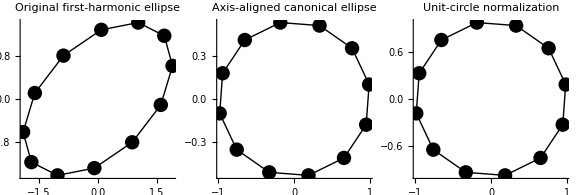

```mathematica
GraphicsRow[
  {
    polygonGraphic[originalSamples, "Original first-harmonic ellipse"],
    polygonGraphic[canonicalSamples, "Axis-aligned canonical ellipse"],
    polygonGraphic[normalizedSamples, "Unit-circle normalization"]
  },
  ImageSize -> Large
]
```

## 12. Continuous normalization comparison

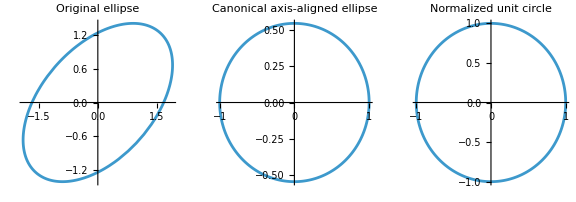

```mathematica
GraphicsRow[
  {
    ellipseCurveGraphic[c1Example, cNExample, Identity, "Original ellipse"],
    ellipseCurveGraphic[
      c1Example,
      cNExample,
      canonicalEllipsePoint[#, normalizationParamsExample] &,
      "Canonical axis-aligned ellipse"
    ],
    ellipseCurveGraphic[
      c1Example,
      cNExample,
      normalizeEllipsePoint[#, normalizationParamsExample] &,
      "Normalized unit circle"
    ]
  },
  ImageSize -> Large
]
```

## 13. Invariants under rotation and scaling

The axis ratio and eccentricity are unchanged by a nonzero complex scaling z↦ηz.

```mathematica
etaExample = 2.4 Exp[0.7 I];
scaledC1 = etaExample c1Example;
scaledCN = etaExample cNExample;

invariantErrors = {
  Abs[N[ellipseAxisRatio[c1Example, cNExample] - ellipseAxisRatio[scaledC1, scaledCN]]],
  Abs[N[ellipseEccentricity[c1Example, cNExample] - ellipseEccentricity[scaledC1, scaledCN]]]
};
invariantQ = Max[invariantErrors] < 10^-10;
```

```mathematica
invariantErrors
```

{2.22045×10^-16,0.}

```mathematica
invariantQ
```

True

## 14. Canonical reconstruction

```mathematica
reconstructFromCanonical[z_, params_Association] :=
  params["MajorAxis"] Exp[I params["Orientation"]] z;

canonicalReconstructionError = Max@Table[
  Abs[N[
    reconstructFromCanonical[
      canonicalEllipsePoint[ellipseCurve[c1Example, cNExample, t], normalizationParamsExample],
      normalizationParamsExample
    ] - ellipseCurve[c1Example, cNExample, t]
  ]],
  {t, 0., 2 Pi, 2 Pi/100}
];
canonicalReconstructionQ = canonicalReconstructionError < 10^-10;
```

```mathematica
canonicalReconstructionError
```

4.96507×10^-16

```mathematica
canonicalReconstructionQ
```

True

## 15. Automated verification report

```mathematica
Clear[verificationReport];

verificationReport[] := verificationReport[20];

verificationReport[maxN_Integer?Positive] := Module[{rows},
  rows = Table[
    Module[{c1, cN, params, axisError, circleError, inverseError, invariantError, eta},
      SeedRandom[7000 + n];
      c1 = RandomReal[{0.8, 2.0}] Exp[I RandomReal[{-Pi, Pi}]];
      cN = RandomReal[{0.1, 0.6}] Exp[I RandomReal[{-Pi, Pi}]];
      params = ellipseNormalizationParameters[c1, cN];
      axisError = Max@Table[
        Abs[N[
          axisAlignedCurve[c1, cN, t] -
          axisAlignedModel[c1, cN, t]
        ]],
        {t, 0., 2 Pi, 2 Pi/40}
      ];
      circleError = Max@Table[
        Abs[N[Abs[normalizedCurve[c1, cN, t, params]] - 1]],
        {t, 0., 2 Pi, 2 Pi/40}
      ];
      inverseError = Max@Table[
        Abs[N[
          inverseNormalizeEllipsePoint[
            normalizeEllipsePoint[ellipseCurve[c1, cN, t], params],
            params
          ] - ellipseCurve[c1, cN, t]
        ]],
        {t, 0., 2 Pi, 2 Pi/40}
      ];
      eta = 1.7 Exp[0.4 I];
      invariantError = Max[{
        Abs[N[ellipseAxisRatio[c1, cN] - ellipseAxisRatio[eta c1, eta cN]]],
        Abs[N[ellipseEccentricity[c1, cN] - ellipseEccentricity[eta c1, eta cN]]]
      }];
      <|
        "n" -> n,
        "Axis-aligned model" -> TrueQ[axisError < 10^-9],
        "Unit-circle normalization" -> TrueQ[circleError < 10^-9],
        "Normalization inverse" -> TrueQ[inverseError < 10^-9],
        "Similarity invariants" -> TrueQ[invariantError < 10^-9]
      |>
    ],
    {n, 3, maxN}
  ];
  Dataset[rows]
];
```

```mathematica
verificationReport[]
```

## Conclusion

The first-harmonic coefficients determine the ellipse completely. Their magnitudes determine the semi-axis lengths, their arguments determine orientation and phase, and a real-linear anisotropic normalization sends every nondegenerate first-harmonic ellipse to the unit circle. Rotation-and-scale invariants such as axis ratio and eccentricity are preserved under complex similarities.